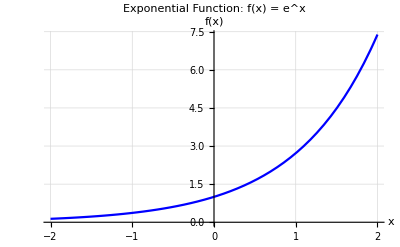

```mathematica
(*Define the exponential function*)
f[x_]:=Exp[x]

(*Plot the exponential function over a specific range*)
Plot[f[x],{x,-2,2},
PlotStyle->Blue,
AxesLabel->{"x","f(x)"},
GridLines->Automatic,PlotLabel->"Exponential Function: f(x) = e^x"
]
```

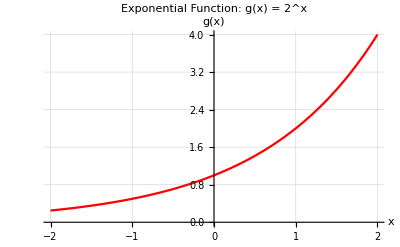

```mathematica
(*Define the exponential function with base 2*)
g[x_]:=2^x

(*Plot the exponential function over a specific range*)
Plot[g[x],{x,-2,2},
PlotStyle->Red,
AxesLabel->{"x","g(x)"},
GridLines->Automatic,PlotLabel->"Exponential Function: g(x) = 2^x"
]
```

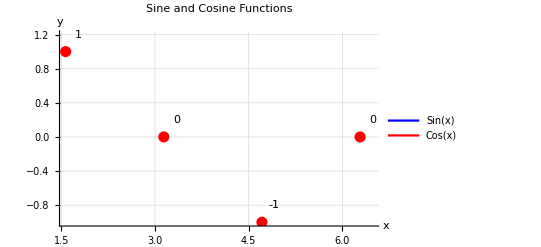

```mathematica
(*Define the sine and cosine functions*)f_sine[x_]:=Sin[x]
f_cosine[x_]:=Cos[x]

(*Plot both functions over a specific range*)
plot=Plot[{f_sine[x],f_cosine[x]},{x,0,2 Pi},PlotStyle->{Blue,Red},AxesLabel->{"x","y"},GridLines->Automatic,PlotLegends->{"Sin(x)","Cos(x)"},PlotLabel->"Sine and Cosine Functions"]

(*Add specific values to the plot using Epilog*)
values={{Pi/2,1},{Pi,0},{3 Pi/2,-1},{2 Pi,0}};(*Example values*)Show[plot,Epilog->{Red,PointSize[0.02],Point[values],Black,Map[Text[#[[2]],#+{0.2,0.2}]&,values]}]
```